# Discrete-time Quantum Walks (PoC)

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,"TwoAhead"]:=ArrayPad[rho,{{0,4},{0,4}}]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#]]&[env["Unitary"][dim+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=(#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#])&[env["Unitary"][dim+1]]},
Inner[Chop[#1*#2[dim+1].state.ConjugateTranspose[#2[dim+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=(#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#])&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*#2[Length[rho]/2+1].state.ConjugateTranspose[#2[Length[rho]/2+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,t],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,2*t],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,t],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,2*t],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
```

## Misc. functions

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=NonlinearModelFit[stdev,A*x,{A},x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
```

## Examples

### Classic random walk

```mathematica
probs=N[Binomial[#,Range[0,#]]/2^#]&/@Range[0,100];
expvals=DTQWPosExpvalue/@probs;
sds=DTQWPosStandardev/@probs;
```

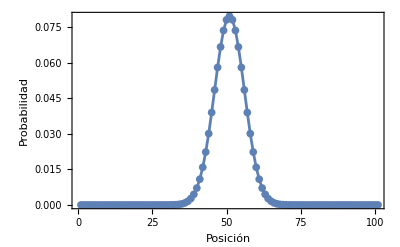

```mathematica
crw=ListLinePlot[probs[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ClassicRandomWalk.pdf",crw]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ClassicRandomWalk.pdf

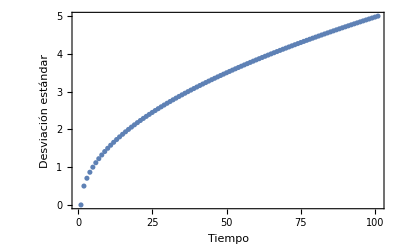

```mathematica
crwm=ListPlot[sds,
PlotRange->All,
Frame->True,
Axes->False,
FrameLabel->{"Tiempo","Desviación estándar"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ClassicRandomWalkSD.pdf",crwm]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ClassicRandomWalkSD.pdf

```mathematica
DTQWSdAdjustments[sds]
```

FittedModel[0.494994 √x]

```mathematica
DTQWSdAdjustments[sds]["AdjustedRSquared"]
```

0.999673

### Unitary DTQW

```mathematica
envC=DTQWEnv[<|"Type"->"ForwardGrowing","Decoherent"->False,"Unitary"->UnitaryOperator|>]
```

DTQWEnv[…]

```mathematica
coinC={1,ⅈ}/Sqrt[2.];
AbsoluteTiming[stepsC=DTQWTrace[coinC,100,envC];]
```

{0.636357,Null}

```mathematica
probsC=DTQWPosDistribution/@stepsC;
expvalsC=DTQWPosExpvalue/@probsC;
sdsC=DTQWPosStandardev/@probsC;
```

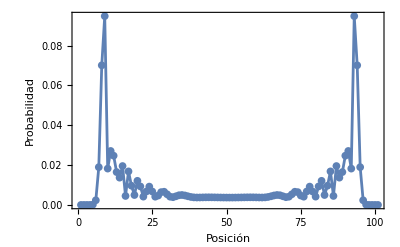

```mathematica
uqw=ListLinePlot[probsC[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/UnitaryQuantumWalk.pdf",uqw]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/UnitaryQuantumWalk.pdf

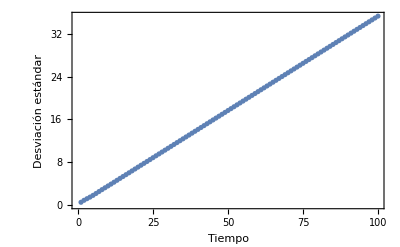

```mathematica
uqwm=ListPlot[sdsC,
PlotRange->All,
Frame->True,
Axes->False,
FrameLabel->{"Tiempo","Desviación estándar"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/UnitaryQuantumWalkSD.pdf",uqwm]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/UnitaryQuantumWalkSD.pdf

```mathematica
DTQWSdAdjustments[sdsC]
```

FittedModel[0.353619 x]

```mathematica
DTQWSdAdjustments[sdsC]["AdjustedRSquared"]
```

0.999998

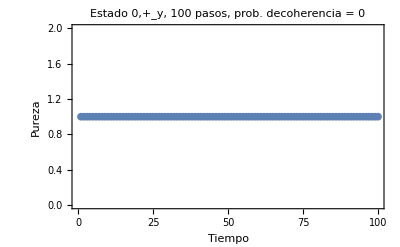

```mathematica
ListLinePlot[Chop[ Tr[#.#]&/@stepsC],
Mesh->All,
Axes->False,
Frame->True,
FrameLabel->{"Tiempo","Pureza"},
PlotLabel->"Estado 0,+_y, 100 pasos, prob. decoherencia = 0"
]
```

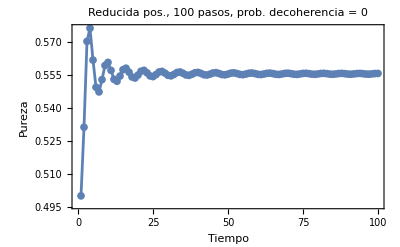

```mathematica
ListLinePlot[Chop[ Tr[#.#]&/@(MatrixPartialTrace[#,2,{Round[Length[#]/2],2}]&/@stepsC)],
Mesh->All,
Axes->False,
Frame->True,
FrameLabel->{"Tiempo","Pureza"},
PlotLabel->"Reducida pos., 100 pasos, prob. decoherencia = 0",
PlotRange->All
]
```

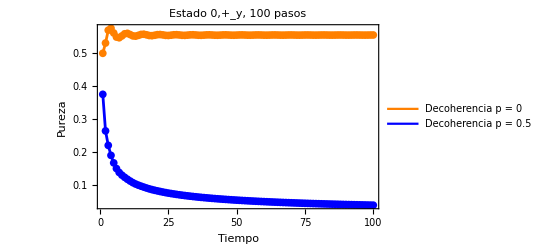

```mathematica
Show[
Legended[%145/.{RGBColor[_,_,_]->Orange},LineLegend[{Orange},{"Decoherencia p = 0"}]],
Legended[%144/.{RGBColor[_,_,_]->Blue},LineLegend[{Blue},{"Decoherencia p = 0.5"}]],
PlotRange->All,
PlotLabel->"Estado 0,+_y, 100 pasos"
]
```

```mathematica
Tr[#.#]&[1/100.IdentityMatrix[100]]
```

0.01

### DTQW w/fuzzy

#### 0.01 Decoherence

```mathematica
envO1=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.99,0.01},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO1={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO1=DTQWTrace[coinO1,100,envO1];]
```

{1.44444,Null}

```mathematica
probsO1=DTQWPosDistribution/@stepsO1;
expvalsO1=DTQWPosExpvalue/@probsO1;
sdsO1=DTQWPosStandardev/@probsO1;
```

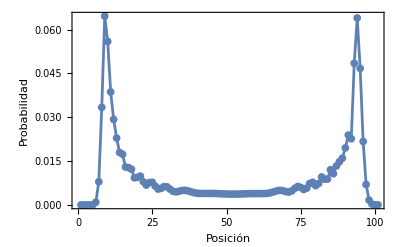

```mathematica
ListLinePlot[probsO1[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_0-01.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_0-01.pdf

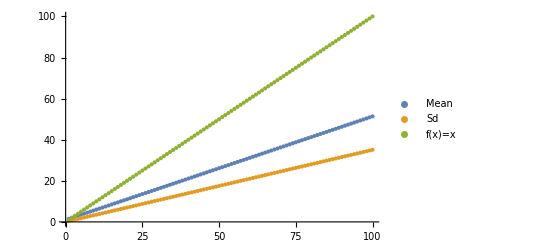

```mathematica
ListPlot[{expvalsO1,sdsO1,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 0.1 Decoherence

```mathematica
envO2=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.9,0.1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
1+1
```

2

```mathematica
coinO2={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO2=DTQWTrace[coinO2,100,envO2];]
```

{1.48733,Null}

```mathematica
probsO2=DTQWPosDistribution/@stepsO2;
expvalsO2=DTQWPosExpvalue/@probsO2;
sdsO2=DTQWPosStandardev/@probsO2;
```

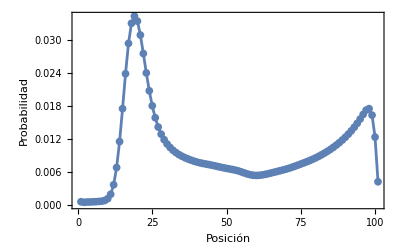

```mathematica
ListLinePlot[probsO2[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_0-1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_0-1.pdf

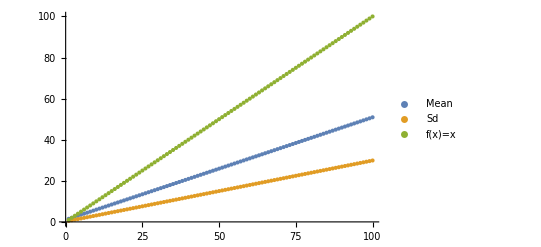

```mathematica
ListPlot[{expvalsO2,sdsO2,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 0.5 Decoherence

```mathematica
envO3=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO3={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO3=DTQWTrace[coinO3,100,envO3];]
```

{1.47646,Null}

```mathematica
probsO3=DTQWPosDistribution/@stepsO3;
expvalsO3=DTQWPosExpvalue/@probsO3;
sdsO3=DTQWPosStandardev/@probsO3;
```

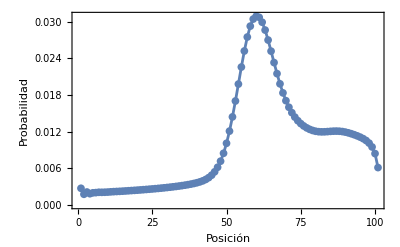

```mathematica
ListLinePlot[probsO3[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_0-5.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_0-5.pdf

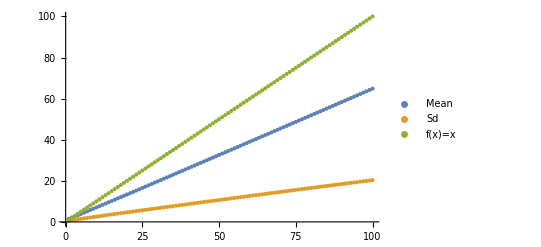

```mathematica
ListPlot[{expvalsO3,sdsO3,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 1 Decoherence

```mathematica
envO4=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0,1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO4={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO4=DTQWTrace[coinO4,100,envO4];]
```

{1.05678,Null}

```mathematica
probsO4=DTQWPosDistribution/@stepsO4;
expvalsO4=DTQWPosExpvalue/@probsO4;
sdsO4=DTQWPosStandardev/@probsO4;
```

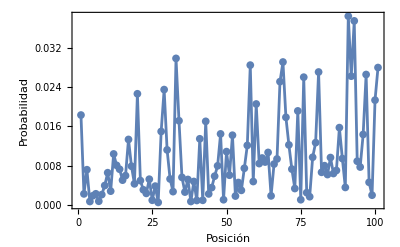

```mathematica
ListLinePlot[probsO4[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/ErrorQW_1.pdf

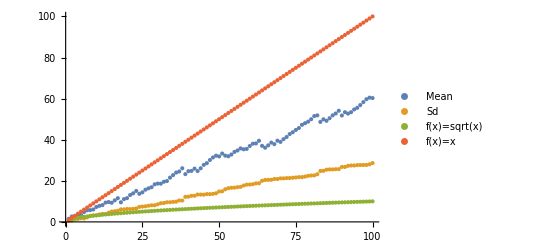

```mathematica
ListPlot[{expvalsO4,sdsO4,Sqrt[Range[100]],Range[100]},
PlotLegends->{"Mean","Sd","f(x)=sqrt(x)","f(x)=x"},
PlotRange->All
]
```

### DTQW w/fuzzy

#### 0.01 Decoherence

```mathematica
envO5=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.99,0.01},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO5={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO5=DTQWTrace[coinO5,100,envO5];]
```

{3.50198,Null}

```mathematica
probsO5=DTQWPosDistribution/@stepsO5;
expvalsO5=DTQWPosExpvalue/@probsO5;
sdsO5=DTQWPosStandardev/@probsO5;
```

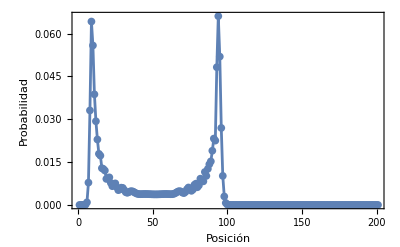

```mathematica
ListLinePlot[probsO5[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_0-01.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_0-01.pdf

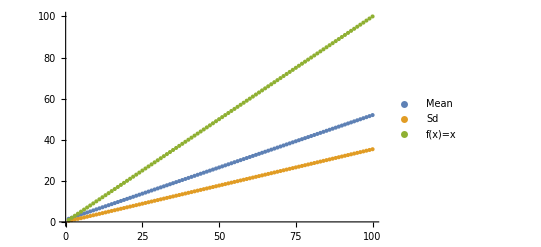

```mathematica
ListPlot[{expvalsO5,sdsO5,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 0.1 Decoherence

```mathematica
envO6=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.9,0.1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO6={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO6=DTQWTrace[coinO6,100,envO6];]
```

{3.93074,Null}

```mathematica
probsO6=DTQWPosDistribution/@stepsO6;
expvalsO6=DTQWPosExpvalue/@probsO6;
sdsO6=DTQWPosStandardev/@probsO6;
```

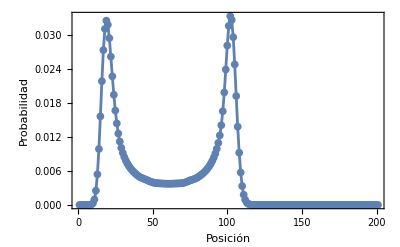

```mathematica
ListLinePlot[probsO6[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_0-1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_0-1.pdf

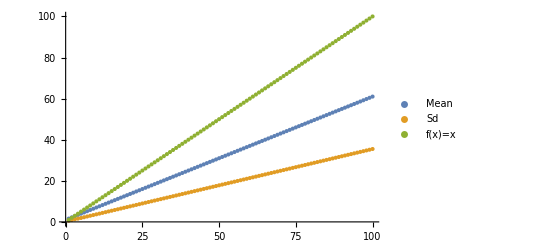

```mathematica
ListPlot[{expvalsO6,sdsO6,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

#### 0.5 Decoherence

```mathematica
envO7=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO7={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO7=DTQWTrace[coinO7,100,envO7];]
```

{4.55738,Null}

```mathematica
probsO7=DTQWPosDistribution/@stepsO7;
expvalsO7=DTQWPosExpvalue/@probsO7;
sdsO7=DTQWPosStandardev/@probsO7;
```

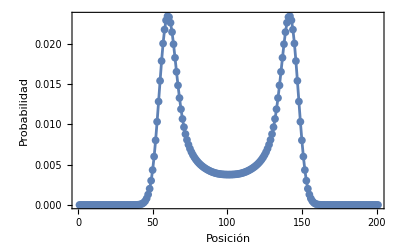

```mathematica
ListLinePlot[probsO7[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_0-5.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_0-5.pdf

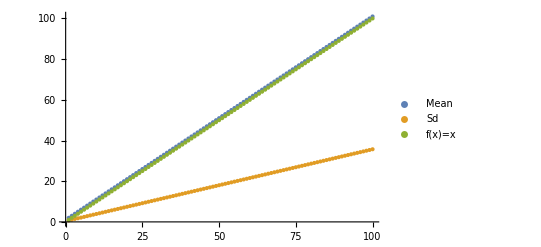

```mathematica
ListPlot[{expvalsO7,sdsO7,Range[100]},
PlotLegends->{"Mean","Sd","f(x)=x"},
PlotRange->All
]
```

```mathematica
DTQWSdAdjustments[sdsO7]
```

FittedModel[0.358843 x]

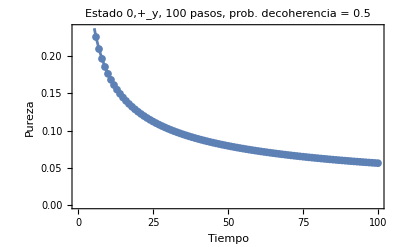

```mathematica
ListLinePlot[Chop[ Tr[#.#]&/@stepsO7],
Mesh->All,
Axes->False,
Frame->True,
FrameLabel->{"Tiempo","Pureza"},
PlotLabel->"Estado 0,+_y, 100 pasos, prob. decoherencia = 0.5"
]
```

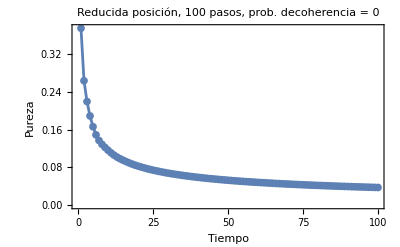

```mathematica
ListLinePlot[Chop[ Tr[#.#]&/@(MatrixPartialTrace[#,2,{Round[Length[#]/2],2}]&/@stepsO7)],
Mesh->All,
Axes->False,
Frame->True,
FrameLabel->{"Tiempo","Pureza"},
PlotLabel->"Reducida posición, 100 pasos, prob. decoherencia = 0",
PlotRange->All
]
```

#### 1 Decoherence

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0,1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>]
```

DTQWEnv[…]

```mathematica
coinO8={1,ⅈ}/Sqrt[2];
AbsoluteTiming[stepsO8=DTQWTrace[coinO8,100,envO8];]
```

{3.09075,Null}

```mathematica
probsO8=DTQWPosDistribution/@stepsO8;
expvalsO8=DTQWPosExpvalue/@probsO8;
sdsO8=DTQWPosStandardev/@probsO8;
```

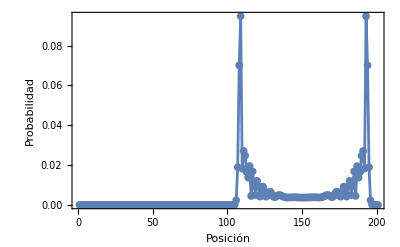

```mathematica
ListLinePlot[probsO8[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_1.pdf

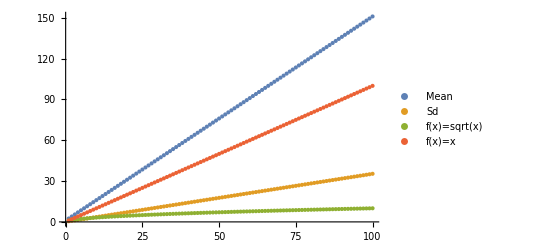

```mathematica
ListPlot[{expvalsO8,sdsO8,Sqrt[Range[100]],Range[100]},
PlotLegends->{"Mean","Sd","f(x)=sqrt(x)","f(x)=x"},
PlotRange->All
]
```

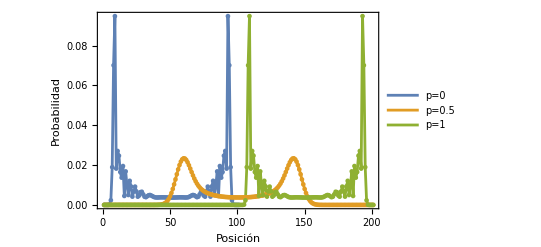

```mathematica
ListLinePlot[{probsC[[-1]],probsO7[[-1]],probsO8[[-1]]},
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"},
PlotLegends->{"p=0","p=0.5","p=1"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_comparative.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_comparative.pdf

### aaa

```mathematica
stepsC[[2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0.375 | 0.216506 | 0.-0.216506 ⅈ | 0.+0.375 ⅈ | 0
0 | 0.216506 | 0.125 | 0.-0.125 ⅈ | 0.+0.216506 ⅈ | 0
0 | 0.+0.216506 ⅈ | 0.+0.125 ⅈ | 0.125 | -0.216506 | 0
0 | 0.-0.375 ⅈ | 0.-0.216506 ⅈ | -0.216506 | 0.375 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
stepsO8[[2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.375 | 0.216506 | 0.-0.216506 ⅈ | 0.+0.375 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.216506 | 0.125 | 0.-0.125 ⅈ | 0.+0.216506 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.+0.216506 ⅈ | 0.+0.125 ⅈ | 0.125 | -0.216506 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.375 ⅈ | 0.-0.216506 ⅈ | -0.216506 | 0.375 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
stepsO7[[2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.09375 | 0.0541266 | 0.-0.0541266 ⅈ | 0.+0.09375 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.0541266 | 0.03125 | 0.-0.03125 ⅈ | 0.+0.0541266 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.+0.0541266 ⅈ | 0.+0.03125 ⅈ | 0.21875 | 0.0541266 | 0.-0.108253 ⅈ | 0.+0.1875 ⅈ | 0 | 0 | 0
0 | 0.-0.09375 ⅈ | 0.-0.0541266 ⅈ | 0.0541266 | 0.15625 | 0.-0.0625 ⅈ | 0.+0.108253 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0.+0.108253 ⅈ | 0.+0.0625 ⅈ | 0.15625 | -0.0541266 | 0.-0.0541266 ⅈ | 0.+0.09375 ⅈ | 0
0 | 0 | 0 | 0.-0.1875 ⅈ | 0.-0.108253 ⅈ | -0.0541266 | 0.21875 | 0.-0.03125 ⅈ | 0.+0.0541266 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.+0.0541266 ⅈ | 0.+0.03125 ⅈ | 0.03125 | -0.0541266 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.09375 ⅈ | 0.-0.0541266 ⅈ | -0.0541266 | 0.09375 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
f[n_]:=Transpose[{Range[0,#],N[Binomial[#,Range[0,#]]/2^#]}]&[n]
```

```mathematica
dist={1,1/2}*#&/@({10,0}+#&/@f[101]);
```

```mathematica
dist1={1,1/2}*#&/@({90,0}+#&/@f[101]);
```

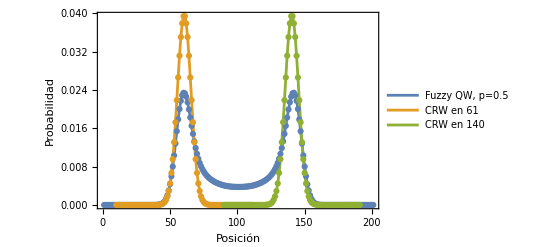

```mathematica
ListLinePlot[{probsO7[[-1]],dist,dist1},
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"},
PlotLegends->{"Fuzzy QW, p=0.5","CRW en 61","CRW en 140"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_adjustingRW.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_adjustingRW.pdf

```mathematica
dist1[[All,2]]+dist[[All,2]]//Total
```

1.